```mathematica
SetDirectory["C:\\Python32\\HeatBumpGUI\\mathematica_output"]
```

C:\Python32\HeatBumpGUI\mathematica_output

```mathematica
a={Import["source_flux_0.dat"],Import["source_flux_333.dat"],Import["source_flux_666.dat"],Import["source_flux_999.dat"],Import["source_flux_1999.dat"],Import["source_flux_2999.dat"],Import["source_flux_3999.dat"],Import["source_flux_4999.dat"]};
```

```mathematica
au={Import["source_flux_0unit.dat"],Import["source_flux_333unit.dat"],Import["source_flux_666unit.dat"],Import["source_flux_999unit.dat"],Import["source_flux_1999unit.dat"],Import["source_flux_2999unit.dat"],Import["source_flux_3999unit.dat"],Import["source_flux_4999unit.dat"]};
```

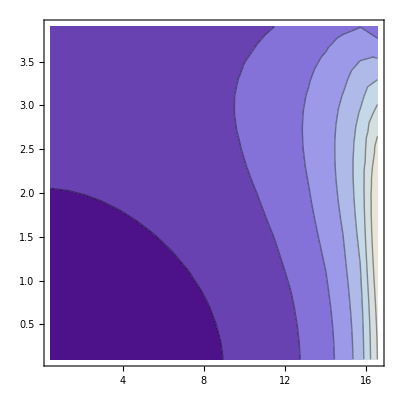
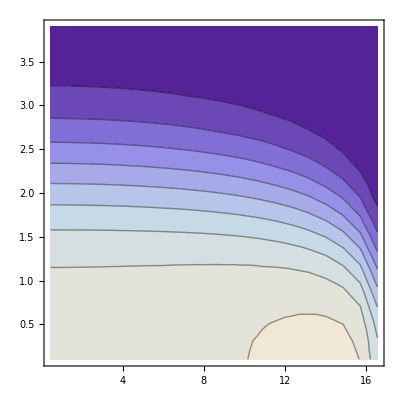
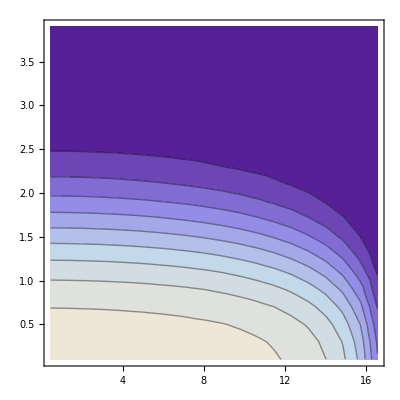
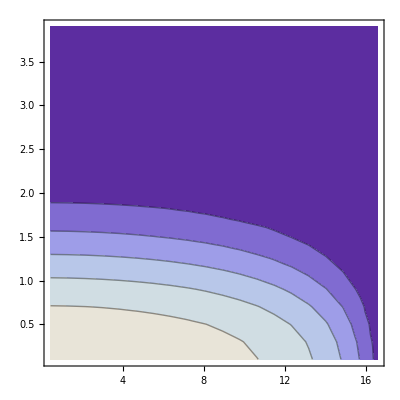
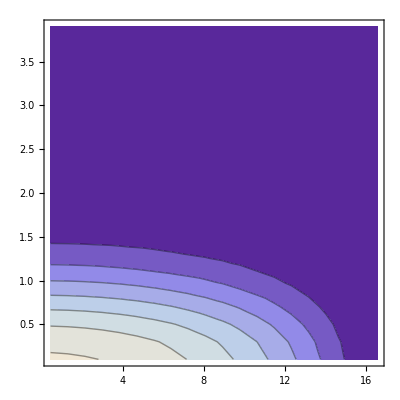
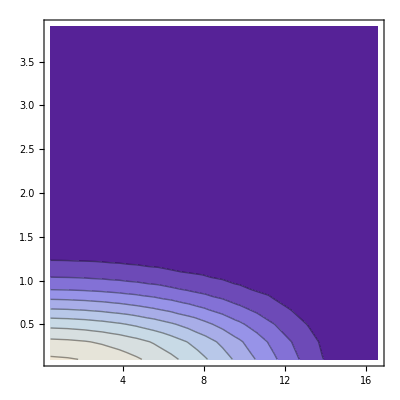
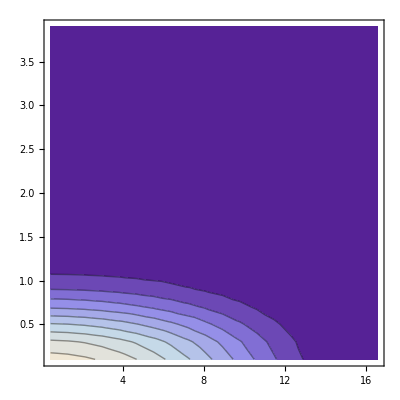
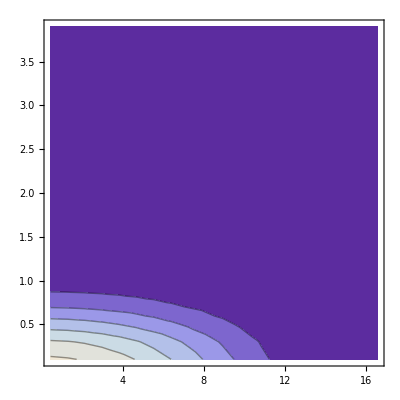
{{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-}}

```mathematica
{ListPlot3D[#,PlotRange->All],ListContourPlot[#,PlotRange->All]}&/@au
```

```mathematica
{ListPlot3D[#,PlotRange->All],ListContourPlot[#,PlotRange->All]}&/@au
```

{{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-}}

-Graphics3D-

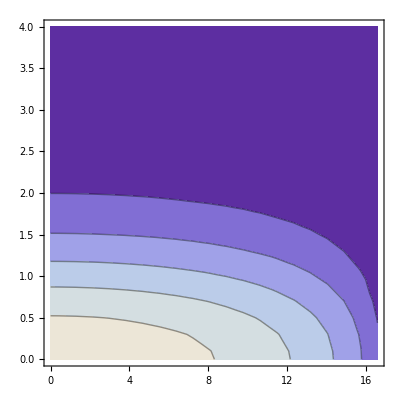

```mathematica
d=Import["power_density.dat"];
ListPlot3D[d]
ListContourPlot[d]
```

```mathematica
fu={Import["filter_flux_0unit.dat"],Import["filter_flux_333unit.dat"],Import["filter_flux_666unit.dat"],Import["filter_flux_999unit.dat"],Import["filter_flux_1999unit.dat"],Import["filter_flux_2999unit.dat"],Import["filter_flux_3999unit.dat"],Import["filter_flux_4999unit.dat"]};
```

```mathematica
f={Import["filter_flux_0.dat"],Import["filter_flux_333.dat"],Import["filter_flux_666.dat"],Import["filter_flux_999.dat"],Import["filter_flux_1999.dat"],Import["filter_flux_2999.dat"],Import["filter_flux_3999.dat"],Import["filter_flux_4999.dat"]};
```

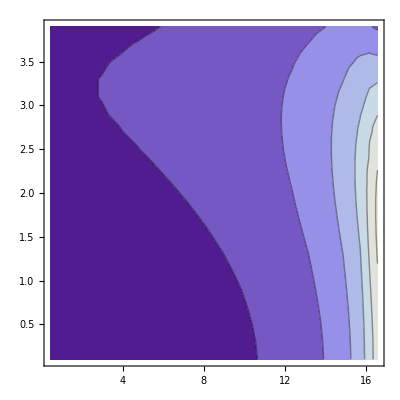
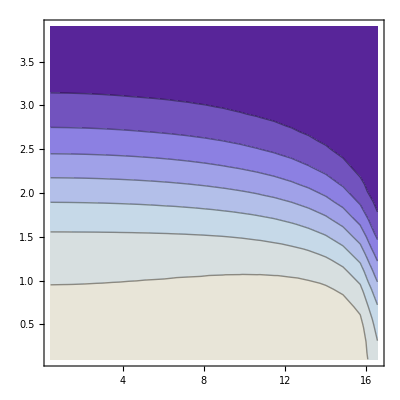
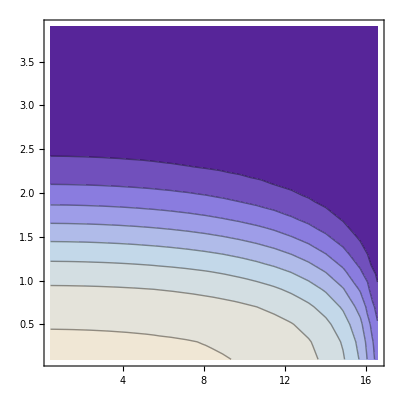
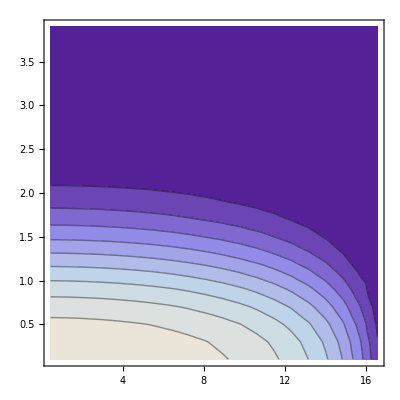
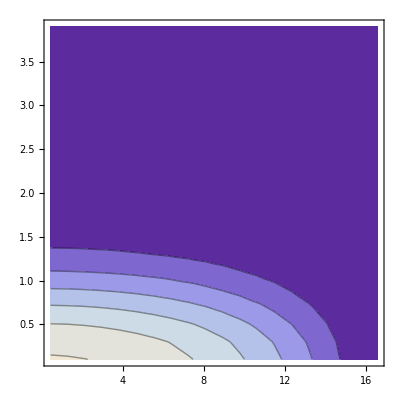
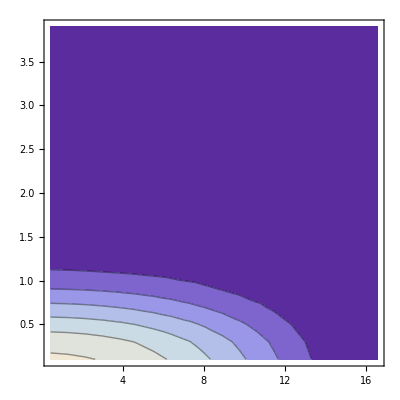
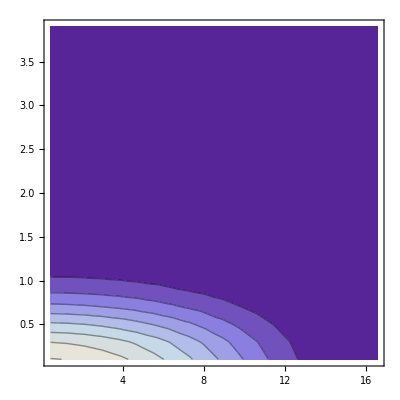
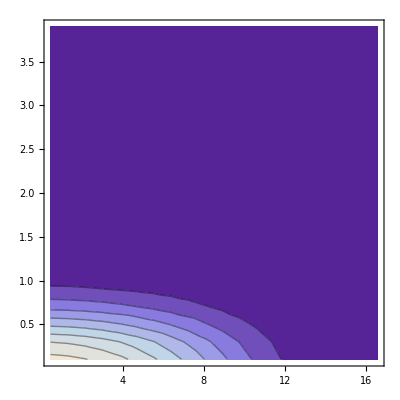
{{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-}}

```mathematica
{ListPlot3D[#,PlotRange->All],ListContourPlot[#,PlotRange->All]}&/@f
```

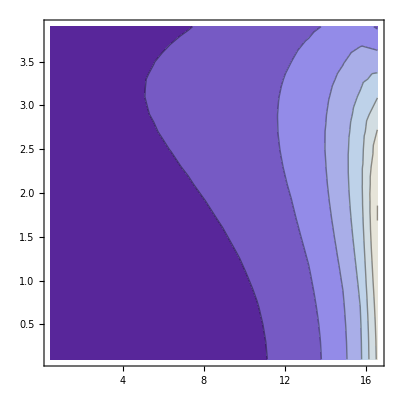
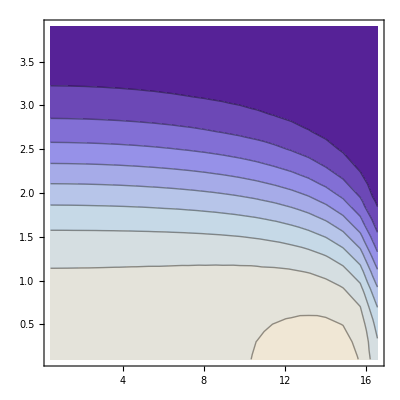
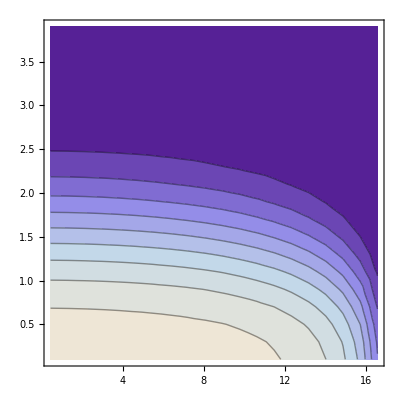
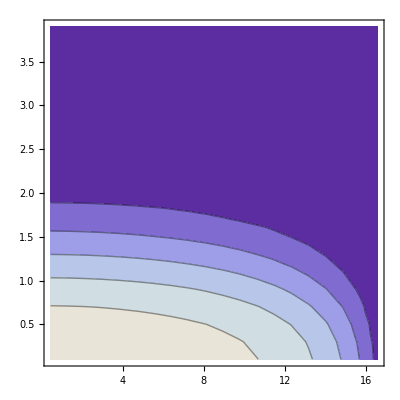
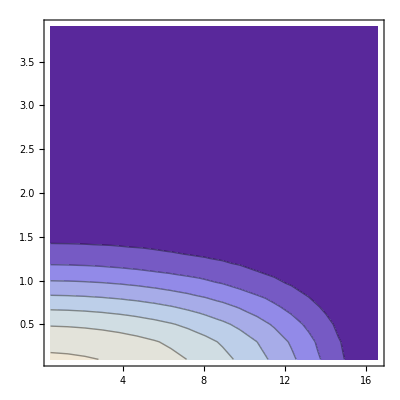
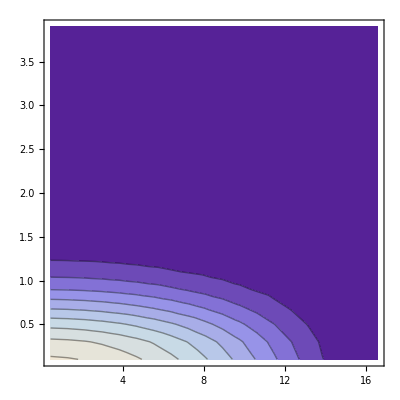
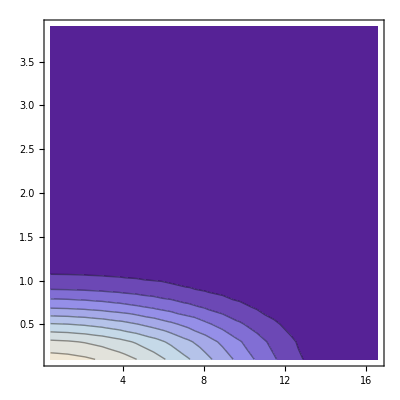
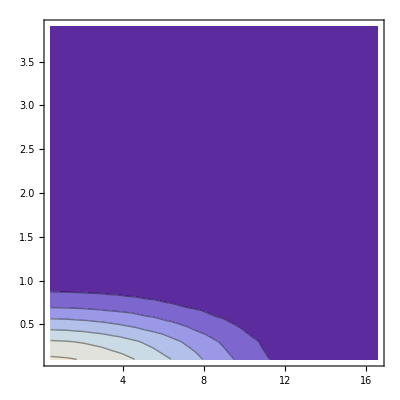
{{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-}}

```mathematica
{ListPlot3D[#,PlotRange->All],ListContourPlot[#,PlotRange->All]}&/@fu
```